x Meters / G/c^2= y Mass
x Meters / (G mass)/c^2= y r_s

```mathematica
G=1
c=1
AU=149597870000
```

1

1

149597870000

```mathematica
rs
```

rs

```mathematica
radius=696340000
mass=1
rs:=(2G mass)/c^2
b=radius
```

696340000

1

696340000

```mathematica
V[u_]:=u^2-2 u^3
```

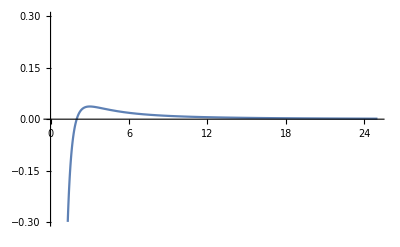

```mathematica
Veff=Plot[V[1/r],{r,0,25},PlotRange->0.3]
```

```mathematica
energy:=Plot[1/b^2,{r,0,25}]
```

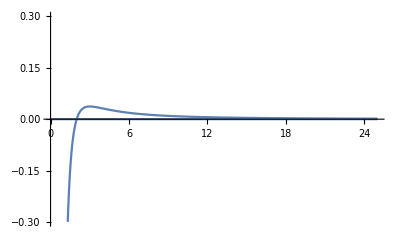

```mathematica
Show[Veff,energy]
```

```mathematica
max=1/3
```

1/3

```mathematica
Vmax=V[max]
```

1/27

```mathematica
theta[r0_,r1_]:=NIntegrate[1/(r^2 √(1/b^2-(1-rs/r)1/r^2)),{r,r0,r1}]
```

```mathematica
delphi=theta[AU,b]
```

-1.56609

```mathematica
u1=AU
u2=b
```

149597870000

696340000

```mathematica
n[z_]:=IntegerPart[z]
zf[z_]:=FractionalPart[z]
```

```mathematica
r[z_]:=u1-z*(u1-u2)
```

```mathematica
phia[z_]:= theta[AU,zf[z](AU-b)+b]
```

```mathematica
accphi[z_]:=theta[u1,u1-z(u1-u2)]
```

```mathematica
x[z_]:=Cos[accphi[z]]r[z]
y[z_]:=Sin[accphi[z]]r[z]
```

```mathematica
fb[theta_,r_,rs_]:=(r Sin[theta])/(√(1-rs/r))
```

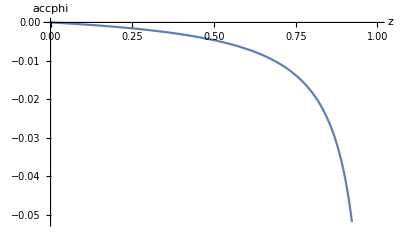

```mathematica
Plot[accphi[z],{z,0,1},AxesLabel->{"z", "accphi"}]
```

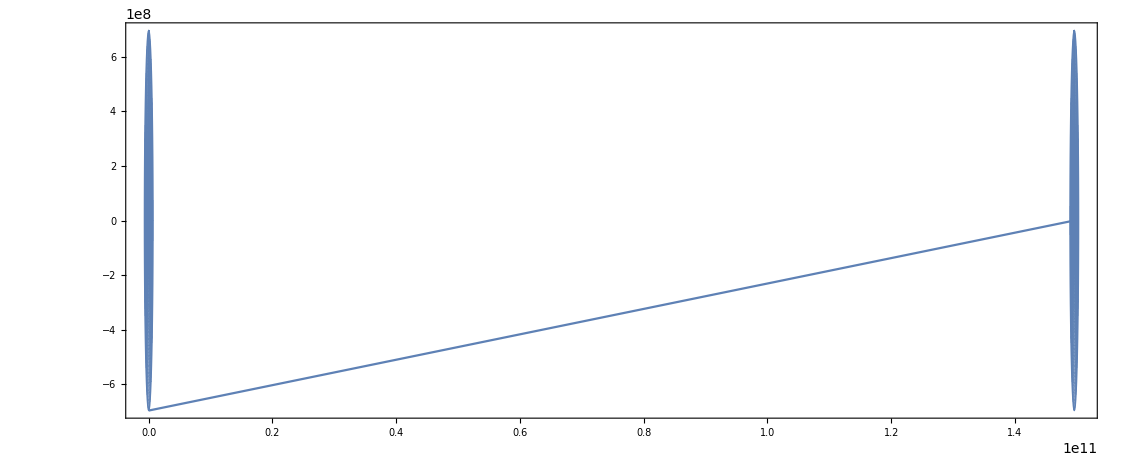

```mathematica
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,radius},Mesh->False];
earth=ParametricPlot[{AU+r Sin[k],r Cos[k]},{k,0,2π},{r,0,radius},Mesh->False];
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
Show[sun,earth,graph,PlotRange->All]
```

```mathematica
u1=1.1rs
u2=20rs
```

2.2

40

```mathematica
b=1.3rs
```

2.6

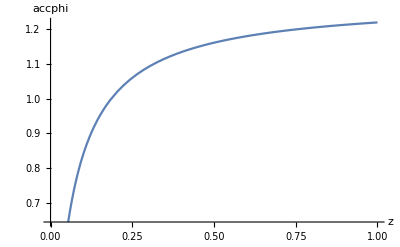

```mathematica
Plot[accphi[z],{z,0,1},AxesLabel->{"z", "accphi"}]
```

```mathematica
theta[u1,u2]
```

1.22018

```mathematica
accphi[0.1]
```

0.839522

```mathematica
Solve[b==r3 √(r3/(r3-rs)),r3]
```

{{r3→1.64789-1.17756 ⅈ},{r3→1.64789+1.17756 ⅈ}}

2

2 ((2/3)^(2/3) (-9 Sin[π/40]^2+√(3 (27 Sin[π/40]^4-32 Sin[π/40]^6)))^(1/3)+(4 Sin[π/40]^2)/((3/2 (-9 Sin[π/40]^2+√(3 (27 Sin[π/40]^4-32 Sin[π/40]^6))))^(1/3)))

2 ((2/3)^(2/3) (-9 Sin[π/20]^2+√(3 (27 Sin[π/20]^4-32 Sin[π/20]^6)))^(1/3)+(4 Sin[π/20]^2)/((3/2 (-9 Sin[π/20]^2+√(3 (27 Sin[π/20]^4-32 Sin[π/20]^6))))^(1/3)))

2 ((2/3)^(2/3) (-9 Sin[(3 π)/40]^2+√(3 (27 Sin[(3 π)/40]^4-32 Sin[(3 π)/40]^6)))^(1/3)+(4 Sin[(3 π)/40]^2)/((3/2 (-9 Sin[(3 π)/40]^2+√(3 (27 Sin[(3 π)/40]^4-32 Sin[(3 π)/40]^6))))^(1/3)))

-(1+ⅈ √3) (-3+√5) (2/(3 (27-9 √5-√(3 (90-34 √5)))))^(1/3)+(1-ⅈ √3)/(3^(2/3) (2/(27-9 √5-√(3 (90-34 √5))))^(1/3))

2 ((2/3)^(2/3) (-9 Sin[π/8]^2+√(3 (27 Sin[π/8]^4-32 Sin[π/8]^6)))^(1/3)+(4 Sin[π/8]^2)/((3/2 (-9 Sin[π/8]^2+√(3 (27 Sin[π/8]^4-32 Sin[π/8]^6))))^(1/3)))

2 ((2/3)^(2/3) (-9 Sin[(3 π)/20]^2+√(3 (27 Sin[(3 π)/20]^4-32 Sin[(3 π)/20]^6)))^(1/3)+(4 Sin[(3 π)/20]^2)/((3/2 (-9 Sin[(3 π)/20]^2+√(3 (27 Sin[(3 π)/20]^4-32 Sin[(3 π)/20]^6))))^(1/3)))

2 ((2/3)^(2/3) (-9 Sin[(7 π)/40]^2+√(3 (27 Sin[(7 π)/40]^4-32 Sin[(7 π)/40]^6)))^(1/3)+(4 Sin[(7 π)/40]^2)/((3/2 (-9 Sin[(7 π)/40]^2+√(3 (27 Sin[(7 π)/40]^4-32 Sin[(7 π)/40]^6))))^(1/3)))

-(1+ⅈ √3) (-5+√5) (2/(3 (45-9 √5-√(3 (10+50 √5)))))^(1/3)+(1-ⅈ √3)/(3^(2/3) (2/(45-9 √5-√(3 (10+50 √5))))^(1/3))

2 ((2/3)^(2/3) (-9 Sin[(9 π)/40]^2+√(3 (27 Sin[(9 π)/40]^4-32 Sin[(9 π)/40]^6)))^(1/3)+(4 Sin[(9 π)/40]^2)/((3/2 (-9 Sin[(9 π)/40]^2+√(3 (27 Sin[(9 π)/40]^4-32 Sin[(9 π)/40]^6))))^(1/3)))

((1+ⅈ √3) (2 (9-√33))^(1/3))/3^(2/3)+(2 2^(2/3) (1-ⅈ √3))/(3 (9-√33))^(1/3)

2 ((2/3)^(2/3) (-9 Cos[(9 π)/40]^2+√(3 (27 Cos[(9 π)/40]^4-32 Cos[(9 π)/40]^6)))^(1/3)+(4 Cos[(9 π)/40]^2)/((3/2 (-9 Cos[(9 π)/40]^2+√(3 (27 Cos[(9 π)/40]^4-32 Cos[(9 π)/40]^6))))^(1/3)))

(1+ⅈ √3) (3+√5) (2/(3 (27+9 √5-√(3 (90+34 √5)))))^(1/3)+(1-ⅈ √3)/(3^(2/3) (2/(27+9 √5-√(3 (90+34 √5))))^(1/3))

$Aborted

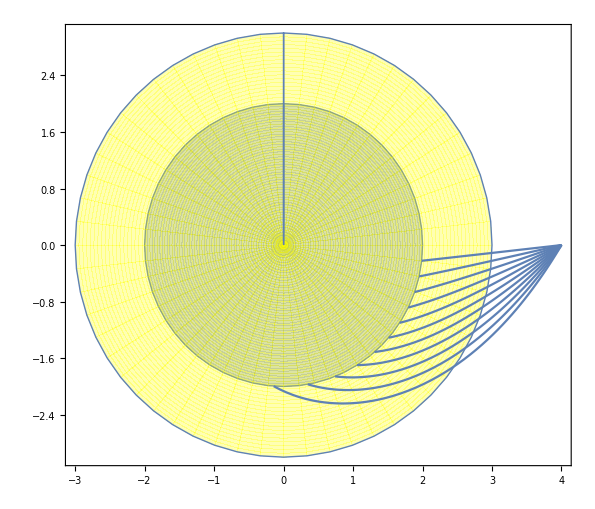

```mathematica
rs
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,rs},Mesh->False];
sphere=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,1.5rs},PlotStyle->Yellow];
plotlist={};
For[j=2,j≤6,j++,
u1=j rs;
For[i=1,i<20,i++,
b=fb[i/40 Pi,u1,rs];
r3=Last@@Last@@Solve[b==r √(r/(r-rs)),r];
Print[r3];
If[Element[r3,Reals]===True,u2=r3,u2=rs];
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
AppendTo[plotlist,graph];
]
]
Show[sun,sphere,plotlist,PlotRange->All]
```

```mathematica
rs
```

2954.03

```mathematica
u1
```

3249.43

```mathematica
b
```

590.806

```mathematica
soln=Solve[b==r √(r/(r-rs)),r]
```

{{r→562.495-774.693 ⅈ},{r→562.495+774.693 ⅈ}}

```mathematica
b
```

590.806

2000

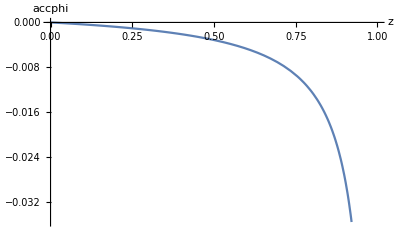

-132.306

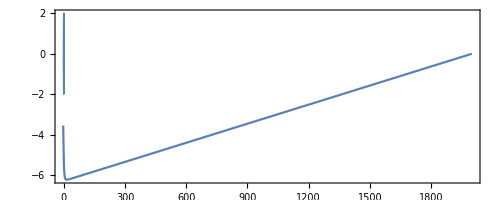

```mathematica
u1=2000
sun=ParametricPlot[{r Sin[k],r Cos[k]},{k,0,2π},{r,0,2},Mesh->False];

b=fb[(1Pi)/1000,2000,rs];
Plot[accphi[z],{z,0,1},AxesLabel->{"z", "accphi"}]
r3=Last@@Last@@NSolve[b==r/(√(1-rs/r)),r];
If[Element[r3,Reals]===True,u2=r3,u2=rs];
Print[theta[u1,u2]/Degree];
graph=ParametricPlot[{x[t],y[t]},{t,0,1},AxesLabel->{"x","y"}];
Show[sun,graph,PlotRange->40]
```

```mathematica
NSolve[b==r/(√(1-rs/r)),r]
```

{{r→4.80195},{r→2.31323}}

```mathematica
N[(3 √3)/2]
```

2.59808

```mathematica
Solve[
```

```mathematica
fb[i,u1,rs]
```

```mathematica
fb[1/10 Pi,10rs,rs]
```

9622.23

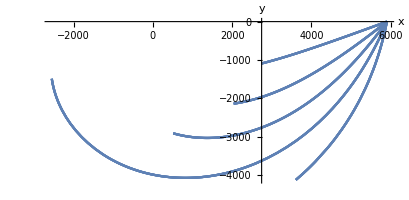

```mathematica
Show[plotlist,PlotRange->All]
```

```mathematica
wtf=Last@@Last@@Solve[b==r √(r/(r-rs)),r]
```

4431.04